# Example 3 - Loading and symmetrising tight-binding models with BandUtilities

Anirudh Chandrasekaran

23 April 2024

## Loading the Library

We first load the library by executing the following:

```mathematica
AppendTo[$Path,StringDelete[NotebookDirectory[],"/Examples"]];
<<BandUtilities`
```

When using the library for other notebooks, copy the folder “Package” on to the folder containing the notebook and add and execute the following lines instead to load the library:

AppendTo[$Path,NotebookDirectory[]<>”Package”];
<<BandUtilities`

## The model

We will use a graphene like model on a fully symmetric honeycomb lattice with nearest and next nearest neighbour hopping. To spice things up a bit, we will also add a staggered chemical potential that makes the two sub-lattices inequivalent. The data is defined as a function in a Wannier90 like format in the following table. The first three entries of each row correspond to the unit cell location, the next two are the orbital index and the last two are respectively the real and imaginary parts of the matrix element.

```mathematica
tbData[t1_,t2_,m_]={{0,0,0,1,2,t1,0},{0,0,0,2,1,t1,0},{0,0,0,1,1,m,0},{0,0,0,2,2,-m,0},{1,0,0,1,2,t1,0},{1,0,0,1,1,t2,0},{1,0,0,2,2,t2,0},{0,-1,0,1,2,t1,0},{0,-1,0,1,1,t2,0},{0,-1,0,2,2,t2,0},{-1,0,0,2,1,t1,0},{-1,0,0,1,1,t2,0},{-1,0,0,2,2,t2,0},{0,1,0,2,1,t1,0},{0,1,0,1,1,t2,0},{0,1,0,2,2,t2,0},
{1,1,0,1,1,t2,0},{1,1,0,2,2,t2,0},
{-1,-1,0,1,1,t2,0},{-1,-1,0,2,2,t2,0}};
```

We export this to a file for a particular choice of t_1,t_2 and m:

```mathematica
Export[NotebookDirectory[]<>"tbm1.dat",tbData[1,0.25,0.25],"CSV"];
```

The routine to build the tight binding model requires us to input the lattice vectors if the lattice is not a square or cubic lattice. Since the data is stored in three dimensional format, we just include a dummy third lattice vector {0,0,1} along with the actual lattice vectors. All this can be avoided by defining the data above with just 2D vectors locating the unit cells and setting “SpaceDimension”→2 as one of the options below. Nevertheless, we use the somewhat unintuitive and long winded route since the data for even 2D models is often stored with 3D vectors in practice (with the third coordinate being 0).

```mathematica
LattVecs={{1/2,(-√3)/2,0},{1/2,(√3)/2,0},{0,0,1}};
```

The Hamiltonian can now be loaded from the file

```mathematica
Hamltn[{k1_,k2_}]=LoadTBM[NotebookDirectory[]<>"tbm1.dat","LatticeVectors"->LattVecs][[1]];
```

Valid lattice vectors provided.

Tight-binding data file loaded.

Space dimension: 3

Number of orbitals: 2

Number of supercells: NoLatticePts$26676

First row of data: {0,0,0,1,2,1,0}

Last row of data: {-1,-1,0,2,2,0.25,0}

Number of entries: 20

Loading Hamiltonian.

No valid symmetrization scheme provided! We will not symmetrize the loaded Hamiltonian.

### Plotting the band structure

To plot the band structure we have to first define the high symmetry points using the reciprocal lattice vectors

```mathematica
G1=((2π Cross[LattVecs[[2]],{0,0,1}])/({0,0,1}.Cross[LattVecs[[1]],LattVecs[[2]]]))[[1;;2]]
G2=((2π Cross[{0,0,1},LattVecs[[1]]])/({0,0,1}.Cross[LattVecs[[1]],LattVecs[[2]]]))[[1;;2]]
```

{2 π,-(2 π)/(√3)}

{2 π,(2 π)/(√3)}

We use one of the M and K points to define the k-path in the Brilluin zone

```mathematica
Mp=G1/2
Kp=(G1+G2)/3
Path1={{{0,0},"Γ"},{Mp,"M"},{Kp,"K"},{{0,0},"Γ"}};
```

{π,-π/(√3)}

{(4 π)/3,0}

Finally we can generate and plot the band structure

```mathematica
BandData1=GenerateBandStructure[Hamltn,Path1];
```

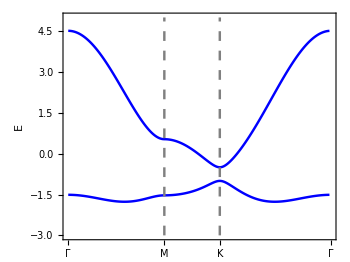

```mathematica
plt1=PlotBandStructure[BandData1,{-3,5}]
```

## Symmetrizing the model while loading it

To see the effect of the symmetrisation, we first observe the model without the staggered chemical potential, which we save to another file:

```mathematica
Export[NotebookDirectory[]<>"tbm2.dat",tbData[1,0.25,0],"CSV"];
```

We can load the new model, setting messages to false (“Messages”→False) to avoid printing comments.

```mathematica
Hamltn2[{k1_,k2_}]=LoadTBM[NotebookDirectory[]<>"tbm2.dat","LatticeVectors"->LattVecs,"Messages"->False][[1]];
```

```mathematica
BandData2=GenerateBandStructure[Hamltn2,Path1];
```

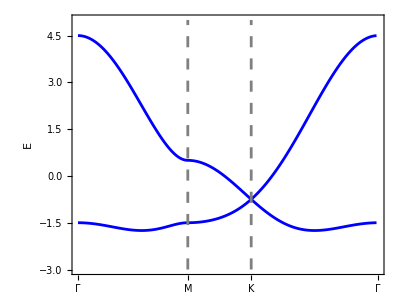

```mathematica
plt2=PlotBandStructure[BandData2,{-3,5}]
```

The C_6 symmetry of the model can be broken precisely by the staggered chemical potential, which kills the nodal point (the linear band crossing at the K point). Let us attempt to use the original data with staggered potential and see if we can symmetrise it to restore the nodal point. Firstly, we need to define a number of ingredients needed for symmetrising the model, like the orbital locations, the real and Hilbert space representations of the symmetry operations. The orbital locations have to be given in the basis where the lattice vectors are unit vectors.

```mathematica
OrbLocs={{2/3,1/3,0},{1/3,2/3,0}};
```

To define the list of symmetries, we have to identify the generating symmetry, its matrix+translation part acting on real space and its representation on the Hilbert space. In this rather simple example, that is a C_6 generator, namely the rotation about the centre of the hexagon by π/6. We assume s like orbitals on each site so that the only effect of the symmetry on the orbitals is to exchange them.

```mathematica
ρ={{1,-1,0},{1,0,0},{0,0,1}}; (*Real space*)
c0={0,0,0}; (*centre of Subscript[C, 6] rotation*)
Uρ={{0,1},{1,0}};

SymmetryList={}; (*This is a multidimensional list which we shall construct below. Each element is a sublist corresponding to a particular symmetry. First element of the sublist is real space symmetry's matrix part, second element is the translation part and the third element is its representation in the Hilbert space. Our point group is Subscript[D, 4], or Subscript[D, 8] in some pepole's notation.*)
Do[
AppendTo[SymmetryList,{MatrixPower[ρ,i],(c0-MatrixPower[ρ,i].c0)//Simplify,MatrixPower[Uρ,i]}];

,{i,1,6}];
```

We can now load the original data in “tbm1.dat” and symmetrise it

```mathematica
Hamltn3[{k1_,k2_}]=LoadTBM[NotebookDirectory[]<>"tbm1.dat","LatticeVectors"->LattVecs,"OrbitalCentres"->OrbLocs,"Symmetries"->SymmetryList][[1]];
```

Valid lattice vectors provided.

Tight-binding data file loaded.

Space dimension: 3

Number of orbitals: 2

Number of supercells: NoLatticePts$29530

First row of data: {0,0,0,1,2,1,0}

Last row of data: {-1,-1,0,2,2,0.25,0}

Number of entries: 20

Loading Hamiltonian.

Valid symmetrization scheme provided! We will symmetrize the loaded Hamiltonian.

Number of supercells after symmetrization: 7

```mathematica
BandData3=GenerateBandStructure[Hamltn3,Path1];
```

```mathematica
plt3=PlotBandStructure[BandData3,{-3,5}]
```

-Graphics-

We see that the nodal point is recovered!